```mathematica
FindFiner[{{1,2,3}}]
```

{{{1},{2,3}},{{1,2},{3}},{{1,3},{2}}}

```mathematica
FindFiner[{{1},{2},{3}}]
```

{}

```mathematica
Compute[start_]:=Block[{todo={start},edges={},current,finer, done={}},
Monitor[
While[Length[todo]>0,
current=First[todo];
todo=Rest[todo];
finer=FindFiner[current];
Table[
AppendTo[edges,PartitionType[current]->PartitionType[part]];

,{part,finer}
];
AppendTo[done,current];
todo=Join[todo,Select[finer,!MemberQ[done,#]&]];
],
{current,Length[todo]}
];
DeleteDuplicates[edges]
]
```

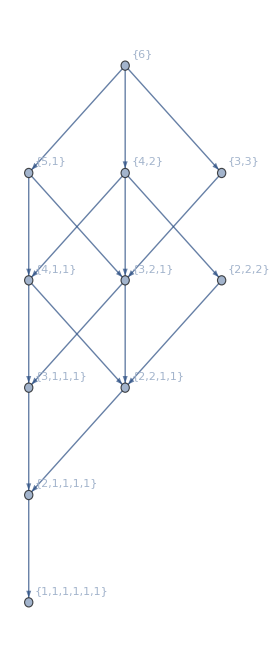

```mathematica
Graph[Compute[{{1,2,3,4,5,6,7}}],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```